```mathematica
{8.71,49.4,0.57}
{4.5,39.4,0.54}
{2.8,37.5,0.53}
```

```mathematica
{-81.8,457.0,0.4}
{-60.7,336.5,0.38}
{-17.2,258.5,0.44}
```

```mathematica
{-87.1,34.9,0.003}
{-59.6,32.4,0.03}
{-27.8,35.0,0.22}
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
f1=ErrorListPlot[{{{{2,8.71},ErrorBar[49.4/(√1000)]},{{3,4.5},ErrorBar[39.4/(√1000)]},{{4,2.8},ErrorBar[37.5/(√1000)]}},{{{2,-87},ErrorBar[457/(√1000)]},{{3,-60},ErrorBar[336/(√1000)]},{{4,-17},ErrorBar[258/(√1000)]}}},PlotRange->{{1,5},{-110,20}},AxesOrigin->{1.5,0},AxesLabel->{"m","W(T)"},PlotLegends->{"$2 player","MG player"}] 
f3=ErrorListPlot[{{{2,-87},ErrorBar[34.9/(√1000)]},{{3,-60},ErrorBar[32/(√1000)]},{{4,-27},ErrorBar[35/(√1000)]}},PlotRange->{{1,5},{50,-120}},AxesOrigin->{1.5,0},AxesLabel->{"m","W(T)"},PlotLegends->{"Market"},PlotStyle->Red]
```

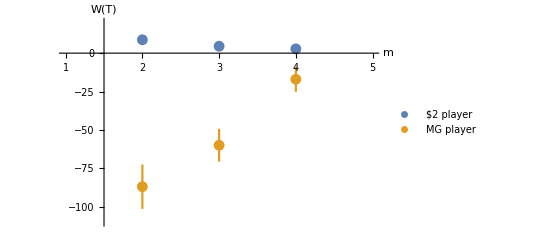

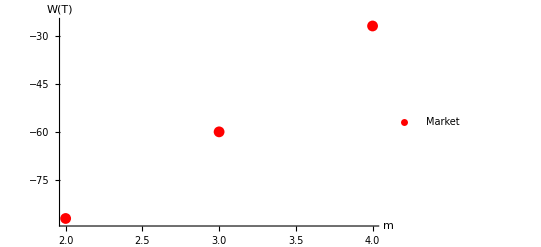

```mathematica
Grid
```

```mathematica
f2=ErrorListPlot[{{{2,-87},ErrorBar[457]},{{3,-60},ErrorBar[336]},{{4,-17},ErrorBar[258]}},PlotRange->{{1,5},{+500,-500}},AxesOrigin->{1.5,0},AxesLabel->{"m","W(T)"},PlotLabel->"MG player"]
```

```mathematica
Data1={{2,0.57},{3,0.54},{4,0.53}};
```

```mathematica
Data2={{2,0.4},{3,0.42},{4,0.44}};
```

{{2,49.4},{3,39,4},{4,37,5}}

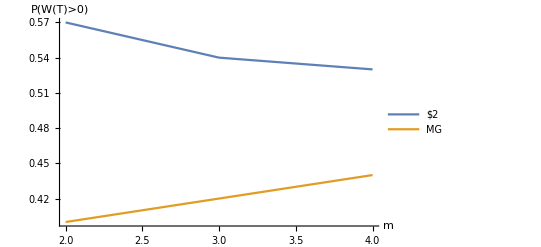

```mathematica
ListPlot[{Data1,Data2},PlotLegends-> {"$2","MG"},AxesLabel->{"m","P(W(T)>0)"},Joined->{True,True}]
```

```mathematica
Data3={{2,49.4},{3,39.4},{4,37.5}}
Data4={{2,457},{3,336},{4,258}}
Data5={{2,34.9},{3,32.4},{4,5}}
```

{{2,49.4},{3,39.4},{4,37.5}}

{{2,457},{3,336},{4,258}}

{{2,34.9},{3,32.4},{4,5}}

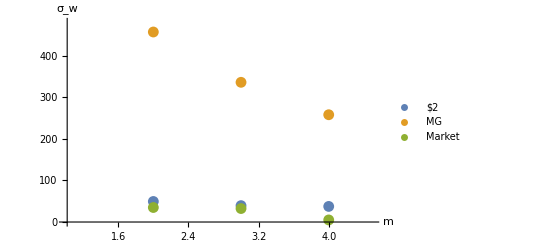

```mathematica
ListPlot[{Data3,Data4,Data5},PlotLegends-> {"$2","MG","Market"},AxesLabel->{"m","σ_w"},PlotRange->{{1,4.5},{0,480}}]
```